# Complex Functions

### Definitions

There are lots of ways to define functions f:ℂ->ℂ.

Taylor Series ∑_(k=0)^∞ (a_k(z-c))^k are useful when they converge i.e. |z-c|<R

Radius of convergence R=(lim_(k->∞) |(a_(k+1))/a_k|)^-1.

You can also use the root test lim_(k->∞) a_k^(1/k).

Analytic Continuation means connecting TS to extend definitions

All your favorite calculus functions extend to ℂ.

You can differentiate and integrate TS.

You can do algebra with TS.

f:ℂ→ℂ is differentiable if f(x+ⅈ y)=u(x,y)+ⅈ v(x,y) and satisfies the Cauchy Riemann (CR) equations

∂_x u | = |    ∂_y v
∂_y u | = | -∂_x v

If f is differentiable then ∂_xx u+∂_yy u | = | ∂_xx v+∂_yy v | =0.  Very useful for solving ∇^2 u=Δu=0. https://en.wikipedia.org/wiki/Potential_flow#Analysis_for_two-dimensional_flow

Differentiable functions f:ℂ→ℂ preserves right angles.   https://en.wikipedia.org/wiki/Conformal_map

```mathematica
f[z_]:= z^(1/4)
TabView[{
"in"->ParametricPlot[ReIm[r E^(ⅈ θ)],{r,0.2,3},{θ,0,2π},
Mesh->All],
"out"->ParametricPlot[ReIm[f[r E^(ⅈ θ)]],{r,0.2,3},{θ,0,2π},
Mesh->All]
},2]
```

12

```mathematica
f[z_]:= z^(1/4)
TabView[{
"in"->ParametricPlot[ReIm[x+ⅈ y],{x,0.2,3},{y,0.5,4},
Mesh->All],
"out"->ParametricPlot[ReIm[f[x+ⅈ y]],{x,0.2,3},{y,0.5,4},
Mesh->All]
},2]
```

12

Such conformal maps are historically useful.  https://en.wikipedia.org/wiki/Joukowsky_transform
https://demonstrations.wolfram.com/JoukowskiAirfoilGeometry

Calculus functions extended to ℂ satisfy the same identities as the calculus functions

Most functions have zero and singularities.

Simple Poles look like 1/(z-z_0).  Double poles look like (z-z_0)^-2…

Zeros of order n  look like (z-z_0)^n.

The coefficient a_-1 sitting atop a pole (a_-1)/(z-z_0) is called a residue.  https://en.wikipedia.org/wiki/Residue_(complex_analysis)

The reason for calling it a_-1 is because it is (z-z_0)^-1 in the Laurent Series ∑_(k=-∞)^(+∞) (a_k(z-z_0))^k

Branch points are where multivalued parts of functions split.  Branch cuts are installed to choose a single branch.

Essential singularity means an isolated singularity that is not a pole.

Differentiable functions on ℂ have lots of names.

Holomorphic: differentiable on some open set in ℂ.

Analytic: Locally given by a convergent TS

Entire: Holomorphic on ℂ.

Lots of identities

Inherited from ℝ

Connecting functions you thought were separate.  For instance, why does tanh have the name it does?

Convergence: Complicated in ℝ.  Simple in ℂ.

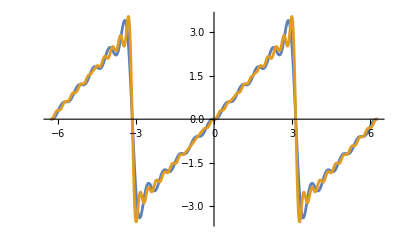

```mathematica
Clear[f,n,x]
f[n_][x_]:=2 Sum[(-1)^(k+1) Sin[k x]/k,{k, 1,n}]
Plot[{f[10][x],f[20][x]},{x,-2π, 2π}]
```

This effect motivates a need for “uniform convergence” in ℝ.

Vitali’s Theorem: In ℂ, if the f_n are analytic and bounded on an open set D⊂ℂ and f_n[z]->f[z] then f[z] is analytic on D.

Functions defined by Integrals

Functions of the form 
	f[z]=∫_a^b g(z,t) dt
are common where the integral is along the straight line connecting a and b in ℂ.  If g is analytic in z and continuous in t then f[z] is analytic.  This still works for a=-∞ and b=∞ as long as the integrals converge.

Example 1: f[z]=∫_0^∞ ⅇ^-t/(1+z t) dt
 
Example 2: Γ[z]=∫_0^∞ ⅇ^-t t^(z-1)dt